```mathematica
Rid = {{1,0},{0,1}};
Rci={{-1/2, -√3/2},{√3/2,-1/2}}; (*123 -> 312 is 120degree added*)
Rac = {{-1/2, √3/2},{-√3/2,-1/2}}; 
(*123 -> 231 is 120degree subtracted*)
R12 = {{Cos[t],Sin[t]},{Sin[t],-Cos[t]}};
R23 = TrigReduce[R12.Rci];
R13 = TrigReduce[R12.Rac];
```

```mathematica
TrigReduce[R23.R23==Rid]
```

True

```mathematica
TrigReduce[R23.R13==Rci]
```

True

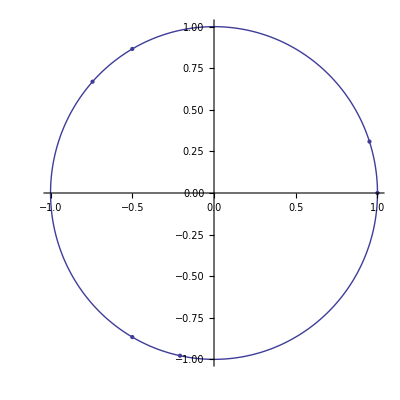

```mathematica
t=0.1*Pi;
Show[ListPlot[{{1,0},Rci.{1,0},Rac.{1,0},R12.{1,0},R23.{1,0},R13.{1,0}}],ParametricPlot[{Cos[x],Sin[x]},{x,0,2*Pi}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```